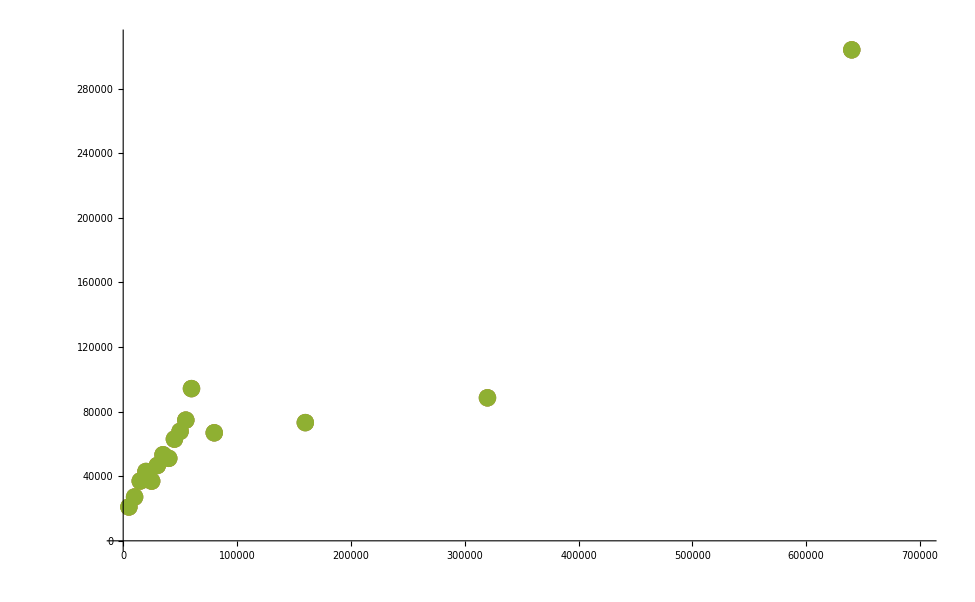

```mathematica
x = {5000, 10000,15000, 20000, 25000, 30000, 35000, 40000,45000, 50000, 55000,60000, 80000, 160000, 320000, 640000};
y = {20950, 27130, 37030, 42910, 36960, 46650, 53280, 51060, 62960, 67790, 74720, 94240, 66880, 73190, 88540, 303980};
std = {}/Sqrt[10];
ListPlot[  {Transpose[{x,y}], Transpose[{x, y+0}],Transpose[{x, y-0}]  }, PlotRange-> {{0, 700000},{0, 310000}}]
```

```mathematica
y+std
```

{26286.,38166.,62517.,78959.,202213.}

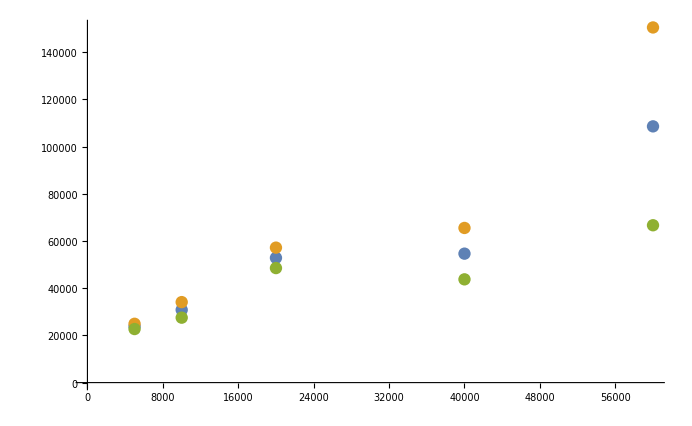

```mathematica
ListPlot[{Transpose[{x,y}], Transpose[{x, y+std}],Transpose[{x, y-std}]}]
```

```mathematica
y = {23800.0, 30800.0, 52840.0, 54620.0, 108540.0}
oldstd = {2486, 7366, 9677, 24339, 93673}
```